```mathematica
(* occmax = 8 *)
```

{a→0.0000239786,b→6.44857}

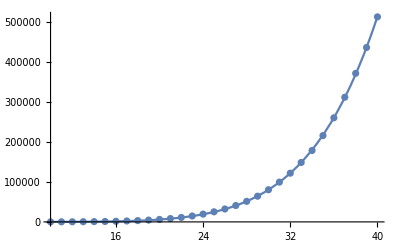

```mathematica
(* Basis size vs. Energy *)
x=Range[10,40];
y={116,186,293,460,706,1049,1590,2297,3261,4520,6170,8342,11157,14796,19471,25219,32287,40921,51419,64301,80421,99476,121851,148587,178643,215834,260320,311748,371498,436206,512821};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

{a→1.0934,b→2.92003}

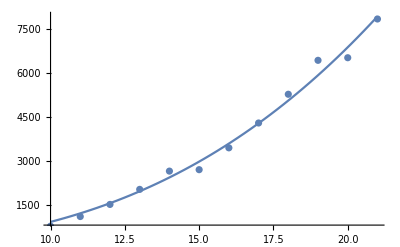

```mathematica
(* Number of operators vs. Energy *)
x={10,11,12,13,14,15,16,17,18,19,20,21};
y={764,1093,1507,2022,2647,2696,3443,4293,5276,6437,6526,7851};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

```mathematica
e=60;
(a*e^b*e/.{a->1.0933998100243698,b->2.920027336701123})
```

1.02136×10^7

{a→0.0000360917,b→7.79506}

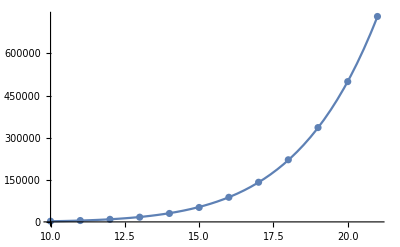

```mathematica
(* Nonzero matrix elements vs. Energy *)
x={10,11,12,13,14,15,16,17,18,19,20,21};
y={2533,4869,9128,16819,30043,51342,87567,141158,221180,335805,499469,731377};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

```mathematica
e=60;
(a*e^b/.{a->0.000036091748759696976,b->7.795057230401028})
(* size in bytes *)
(16*a*e^b/.{a->0.000036091748759696976,b->7.795057230401028})
```

2.61938×10^9

4.19101×10^10